```mathematica
μ=0.62;
γ=5/3;
```

```mathematica
years=365.25*86400;
tEnd=10^3 years;
```

```mathematica
rper=0.7Rsun;
θper=45*Pi/180;
kRoss=21.1;
χ=(16*T[Rper,zper]^3*sigmaSB*(γ-1)*μ*mP)/(3*kRoss*ρ[Rper,zper]^2*kB);  (*this is what Goldreich and Schubert call χ*)
ξradiative = (γ-1)*χ ;    (*this is what Balbus and Schaan call ξrad*)

ν=23;   (*from Menou&Balbus2004*)

η=596;     (*from Menou&Balbus2004*)
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=23;  
η=596;    
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=0.01Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

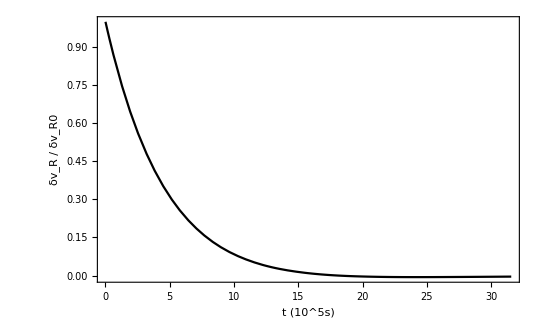

```mathematica
Graphico3=Plot[δvRsol[10^5 t]/δvRsol[0],{t,0,(tEnd/10^5)/10000},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (10^5s)","δv_R / δv_R0 ","ξ_rad = ξ_(rad⊙),  ν = ν_⊙,  η = η_⊙"},BaseStyle->{FontWeight->"Bold",FontSize->12},FrameStyle->Black]
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=2;  
η=596;     
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=0.01Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

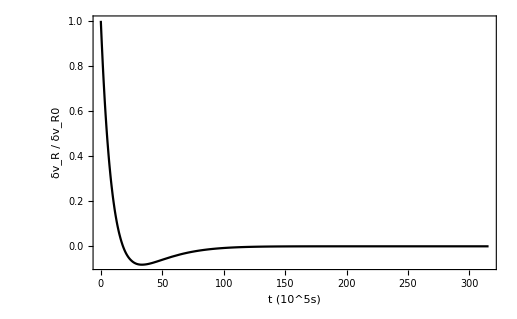

```mathematica
Graphico4=Plot[δvRsol[10^5 t]/δvRsol[0],{t,0,(tEnd/10^5)/1000},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (10^5s)","δv_R / δv_R0 ", "ξ_rad = ξ_(rad⊙),  ν = 0.1ν_⊙,  η = η_⊙"},BaseStyle->{FontWeight->"Bold",FontSize->12},FrameStyle->Black]
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=0;  
η=596;    
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=0.01Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

```mathematica
Graphico5=Plot[δvRsol[10^5 t]/δvRsol[0],{t,0,(tEnd/10^5)/1000},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (10^5s)","δv_R / δv_R0 "},BaseStyle->{FontWeight->"Bold",FontSize->12},FrameStyle->Black];
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=23;  
η=596;    
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=100Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

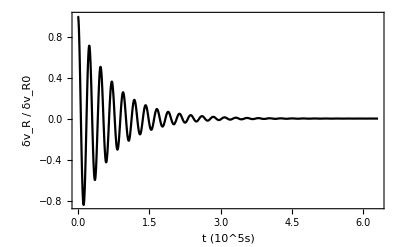

```mathematica
Graphico6=Plot[δvRsol[10^5 t]/δvRsol[0],{t,0,(tEnd/10^5)/50000},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (10^5s)","δv_R / δv_R0 ", "k·v_A = 10^2Ω,  ξ_rad = ξ_(rad⊙),  ν = ν_⊙,  η = η_⊙"},BaseStyle->{FontWeight->"Bold",FontSize->12},FrameStyle->Black]
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=23;  
η=60;     
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=100Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

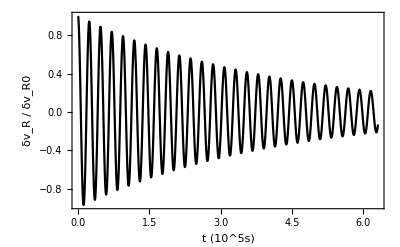

```mathematica
Graphico7=Plot[δvRsol[10^5 t]/δvRsol[0],{t,0,(tEnd/10^5)/50000},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (10^5s)","δv_R / δv_R0 ","k·v_A = 10^2Ω,  ξ_rad = ξ_(rad⊙),  ν = ν_⊙,  η = 0.1η_⊙"},BaseStyle->{FontWeight->"Bold",FontSize->12},FrameStyle->Black]
```

```mathematica
(*Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic3.png",Graphico3];
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic4.png",Graphico4];
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic6.png",Graphico6];
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic7.png",Graphico7];*)
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=23;  
η=596;     
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=1Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

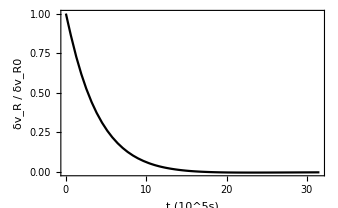

```mathematica
Graphico8=Plot[δvRsol[10^5 t]/δvRsol[0],{t,0,(tEnd/10^5)/10000},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (10^5s)","δv_R / δv_R0 "},BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

```mathematica
1/Ω[Rper,zper]
```

377013.